```mathematica
i0=ImportString["0 
309 
418 
424 
0 
181 
83 
0 
423 
497 
901 
1312 "]//Flatten
```

{0,309,418,424,0,181,83,0,423,497,901,1312}

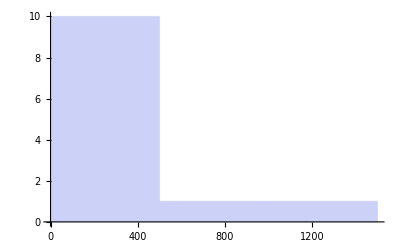

```mathematica
Histogram[i0]
```

```mathematica
i1=ImportString["192 
156 
71 
0 
130 
0 
0 
82 
126 
133 
0 
0 
102 
0 
0 
124 
160 
163 
49 
142 
175 
441 
123 
223 
0 
131 
75 
226 
79 
39 
0 
101 
483 
0 
122 
141 
117 
266 
138 
74 
71 
171 
584 
175 
147 
26 
33 
0 
328 
451 
99 
222 
169 
133 
162 
458 
216 
15 
125 
67 
102 
125 
0 
130 
163 
45 
102 
31","Table"]//Flatten
```

{192,156,71,0,130,0,0,82,126,133,0,0,102,0,0,124,160,163,49,142,175,441,123,223,0,131,75,226,79,39,0,101,483,0,122,141,117,266,138,74,71,171,584,175,147,26,33,0,328,451,99,222,169,133,162,458,216,15,125,67,102,125,0,130,163,45,102,31}

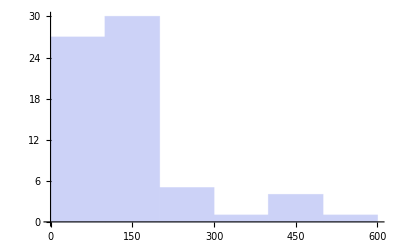

```mathematica
Histogram[i1]
```

```mathematica
ii=ImportString["0 
309 
418 
424 
0 
181 
83 
0 
423 
497 
901 
1312 
192 
156 
71 
0 
130 
0 
0 
82 
126 
133 
0 
0 
102 
0 
0 
124 
160 
163 
49 
142 
175 
441 
123 
223 
0 
131 
75 
226 
79 
39 
0 
101 
483 
0 
122 
141 
117 
266 
138 
74 
71 
171 
584 
175 
147 
26 
33 
0 
328 
451 
99 
222 
169 
133 
162 
458 
216 
15 
125 
67 
102 
125 
0 
130 
163 
45 
102 
31 
194 
619 
369 
545 
478 
0 
67 
0 
0 
607 
0 
376 
94 
44 
0 
74 
0 
1148 
26 
33 
145 
244 
330 
162 
0 
996 
157 
251 
75 
210 
1226 
631 
0 
283 
89 
1422 
525 
342 
119 
201 
0 
238 
0 
386 
686 
655 
762 
0 
443 
284 
109 
498 
0 
726 
432 
160 
124 
160 
970 
346 
1108 
606 
151","Table"]//Flatten
```

{0,309,418,424,0,181,83,0,423,497,901,1312,192,156,71,0,130,0,0,82,126,133,0,0,102,0,0,124,160,163,49,142,175,441,123,223,0,131,75,226,79,39,0,101,483,0,122,141,117,266,138,74,71,171,584,175,147,26,33,0,328,451,99,222,169,133,162,458,216,15,125,67,102,125,0,130,163,45,102,31,194,619,369,545,478,0,67,0,0,607,0,376,94,44,0,74,0,1148,26,33,145,244,330,162,0,996,157,251,75,210,1226,631,0,283,89,1422,525,342,119,201,0,238,0,386,686,655,762,0,443,284,109,498,0,726,432,160,124,160,970,346,1108,606,151}

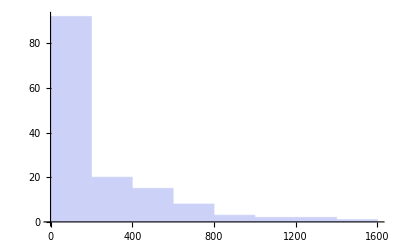

```mathematica
Histogram[ii]
```

```mathematica
i3=ImportString["0 
67 
0 
0 
607 
0 
376 
94 
44 
0 
74 
0 
1148 
26 
33 
145 
244 
330 
162 
0 
996 
157 
251 
75 
210 
1226 
631 
0 
283 ","Table"]//Flatten
```

{0,67,0,0,607,0,376,94,44,0,74,0,1148,26,33,145,244,330,162,0,996,157,251,75,210,1226,631,0,283}

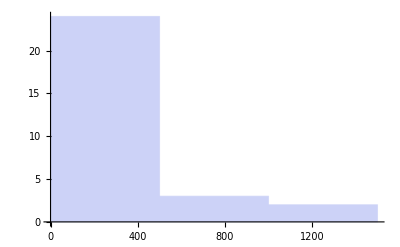

```mathematica
Histogram[i3]
```

```mathematica
i2=ImportString["194 
619 
369 
545 
478 ","Table"]//Flatten
i4=ImportString["89 
1422 
525 
342 
119 
201 
0 
238 
0 
386 
686 
655 
762 
0 
443 
284 
109 
498 ","Table"]//Flatten
```

{194,619,369,545,478}

{89,1422,525,342,119,201,0,238,0,386,686,655,762,0,443,284,109,498}

```mathematica
i5=ImportString["0 
726 
432 
160 
124 
160 
970 
346 
1108 
606 
151 ","Table"]//Flatten
```

{0,726,432,160,124,160,970,346,1108,606,151}

```mathematica
FindDistributionParameters[ii,ExponentialDistribution[λ]]
```

{λ→0.00415601}

```mathematica
DistributionFitTest[ii,ExponentialDistribution[0.0041560102301790285],"TestConclusion"]
```

The null hypothesis that the data is distributed according to the ExponentialDistribution[0.00415601] is rejected at the 5 percent level based on the Cramér-von Mises test.

```mathematica
h["TestDataTable",All]
```

| Statistic | P-Value
Anderson-Darling | 715.102 | 0.
Cramér-von Mises | 0.642335 | 0.0176073
Pearson χ^2 | 59.1329 | 1.66411×10^-7

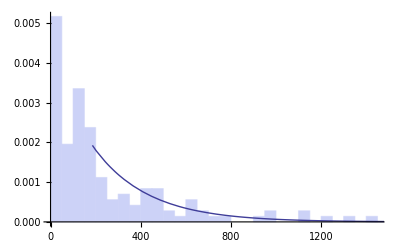

```mathematica
Show[
Histogram[ii,20,"ProbabilityDensity"],
Plot[PDF[ExponentialDistribution[0.0041560102301790285],x],{x,0,2000}]
]
```

```mathematica
FindDistributionParameters[i0,ExponentialDistribution[λ0]]
FindDistributionParameters[i1,ExponentialDistribution[λ1]]
FindDistributionParameters[i2,ExponentialDistribution[λ2]]
FindDistributionParameters[i3,ExponentialDistribution[λ3]]
FindDistributionParameters[i4,ExponentialDistribution[λ4]]
FindDistributionParameters[i5,ExponentialDistribution[λ5]]
```

{λ0→0.00263852}

{λ1→0.00761137}

{λ2→0.00226757}

{λ3→0.00403956}

{λ4→0.00266312}

{λ5→0.00229981}

```mathematica
0.015057283142389525/0.0076113722856503245
```

1.97826

```mathematica
I1=ImportString["176 
0 
120 
34 
48 
206 
57 
150 
6 
103 
306 
20 
214 
204 
74 
142 
67 
21 
172 
2 
69 
18 
62 
11 
76 
10 
6 
63 
63 
102 
15 
52 
58 
45 
60 
17 
18 
15 
49 
77 
10 
15 
18 
11 
49 
157 
10 
46 
160 
69 
89 
115 
1 
210 
12 
47 
3 
62 
141 
32 
142 
20 
26 
126 
11 
61 
58 
2 
57 
132 
21 
205 
49 
25 
15 
37 
42 
19 
19 
139 
91 
14 
85 
11 
64 
73 
18 
23 
33 
24 
20 
183 ","Table"]//Flatten
```

{176,0,120,34,48,206,57,150,6,103,306,20,214,204,74,142,67,21,172,2,69,18,62,11,76,10,6,63,63,102,15,52,58,45,60,17,18,15,49,77,10,15,18,11,49,157,10,46,160,69,89,115,1,210,12,47,3,62,141,32,142,20,26,126,11,61,58,2,57,132,21,205,49,25,15,37,42,19,19,139,91,14,85,11,64,73,18,23,33,24,20,183}

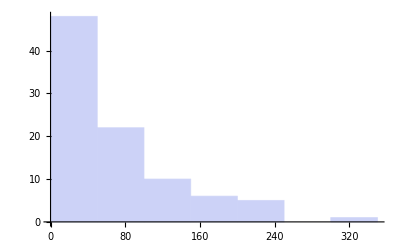

```mathematica
Histogram[I1]
```

```mathematica
FindDistributionParameters[I1,ExponentialDistribution[λ]]
```

{λ→0.0150573}

```mathematica
DistributionFitTest[I1,ExponentialDistribution[0.015057283142389525]]
```

0.690963

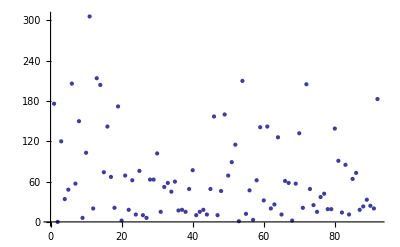

```mathematica
ListPlot[I1]
```